# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG"; 
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wymiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(* tensor metryczny bez perturbacji *)
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];*)

(* czy zmienne Mukhanova-Sasakiego stosować *)
mMS=True;
(*mMS=False;*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=2;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ,χ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
(* R^2 arXiv:1705.03023 *)
(*fG=Table[Which[ I == J && I==1, 1,I == J && I==2, ϕ^2, True , 0 ],{I ,1,lpol } ,{J ,1,lpol }];*)
(* H^2 arXiv:1705.03023, arXiv:1707.05125v1 *)
fG=Table[Which[ I == J && I==1, 1,I == J && I==2, L^2*Sinh[ϕ/L]^2, True , 0 ],{I ,1,lpol } ,{J ,1,lpol }];

(* lagranżjan z artykułu arXiv:1401.6163v3 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
(* 1 arXiv:1707.05125v1 *)
fun={V->(Subscript[V, 0] Exp[λ*#1] &)};
param=Rationalize[{L->10^(-2),Subscript[V, 0]->10^(-4),λ->1}];
(* 2 arXiv:1707.05125v1 *)
(*fun={V->(m^2*#1^2/2 &)};
param=Rationalize[{L->10^(-2),m->10^(-2)}];*)
(* arXiv:1705.03023 *)
(*fun={V->(α^2(1+β*#1+η*#1^2/2) &)};
param=Rationalize[{L->10^(-2),α->10^(-20),β->10^(-15),η->10^(-2)}];*)
(*param=Rationalize[{L->10^(-2),α->10^(-20),β->10^(-5),η->10^(-2)}];*)

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\hyper\\1";
(*sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\hyper\\2";*)
(*sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\hyper";*)
nazwaplikurow="hyper2";
```

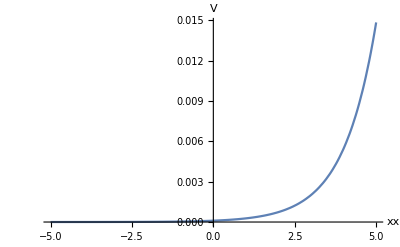

```mathematica
(* potencjał *)
VT[x1_]:=V[x1] /.fun /. param
Plot[Evaluate[VT[xx]],{xx,-5,5},AxesLabel->{xx,V},PlotRange->All]
```

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
warunki={L>0,pola[[1]][x[[1]]]>0};
```

```mathematica
(* tensor metryczny w longitudinal gauge *)
Block[{Lag,Masa,ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* gęstość lagranżjanu *)
Lag=ℒ==Lagrangian[g,x,pola,fG,La,0];
(* macierz masy *)
Masa=MacierzMasy[g,x,pola,fG,La,False];
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=RuchuRownaniakw[g,x,pola,fG,La,1];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=If[mMS,MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1],False];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La,False];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,mMS,1,True],600,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,mMS,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Lagranżjan",Lag},{"Macierz masy",Masa},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Lagranżjan",Lag},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"F",sciezka];
wpisB={"Macierz masy",Masa};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"M",sciezka];
)]//AbsoluteTiming
```

00:11:58GMT+2.TimeObject[{0,11,58.8761},TimeZone→2.] Równania ruchu w rzędzie 0

00:12:08GMT+2.TimeObject[{0,12,8.61883},TimeZone→2.] Równania ruchu w rzędzie 0

00:12:15GMT+2.TimeObject[{0,12,15.3946},TimeZone→2.] Równanie pola 00 w rzędzie 0

00:12:15GMT+2.TimeObject[{0,12,15.517},TimeZone→2.] Równania ruchu w rzędzie 1

00:12:19GMT+2.TimeObject[{0,12,19.0806},TimeZone→2.] Równania ruchu w rzędzie 1

00:12:30GMT+2.TimeObject[{0,12,30.4742},TimeZone→2.] Równanie pola 00 w rzędzie 1

00:12:32GMT+2.TimeObject[{0,12,32.3506},TimeZone→2.] Równanie pola 01 w rzędzie 1

00:12:32GMT+2.TimeObject[{0,12,32.7864},TimeZone→2.] Równanie pola 11 w rzędzie 0

00:12:33GMT+2.TimeObject[{0,12,33.0056},TimeZone→2.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

00:15:10GMT+2.TimeObject[{0,15,10.1184},TimeZone→2.] Baza Freneta

00:15:12GMT+2.TimeObject[{0,15,12.6532},TimeZone→2.] Baza Freneta

00:15:12GMT+2.TimeObject[{0,15,12.9519},TimeZone→2.] Pochodne potencjału w zmiennych σ i s

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

00:15:17GMT+2.TimeObject[{0,15,17.5446},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

00:18:53GMT+2.TimeObject[{0,18,53.2966},TimeZone→2.] Równania ruchu dla zmiennych współporuszających się

{415.359,Null}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tfTot}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* całkowita liczba e-powiększeń - NALEŻY USTAWIĆ! *)
Nall=15.;
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
wstepneWP={{0.5603,0.},{-0.000229,1.2*10^(-25)}}; (* 1 *)
wstepneWSP={{0.,0.},{0.,0.}};
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

00:20:49GMT+2.TimeObject[{0,20,49.5936},TimeZone→2.]

{ϕ[0.]==0.5603,χ[0.]==0.,ϕ'[0.]==-0.000229,χ'[0.]==1.2×10^-25,nn[0.]==0.}

$Aborted

```mathematica
{tloi,Ntot, tfTot}=Rationalize[{{{0.5603,0.},{-0.000229,1.20*10^(-25)}},80.,10^4},10^(-25)];(*1*)
(*{tloi,Ntot, tfTot}=Rationalize[{{{0.6925,0.},{-0.00008482,1.393*10^(-31)}},80.,10^4},10^(-31)];(*2*)*)
```

```mathematica
%//N
```

{{{0.5603,0.},{-0.000229,1.2×10^-25}},80.,10000.}

```mathematica
(* końcowy czas *)
tf=tfTot;
tf=3*10^3; (* 1 *)
(*tf=2*10^4;  (* 2 *)*)
```

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
N0t=-8.;
N0p=N0t;
```

### Tło

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,{tf},fun,param,sciezka,N0t];//AbsoluteTiming
```

14:16:25GMT+2.TimeObject[{14,16,25.8042},TimeZone→2.]

14:16:27GMT+2.TimeObject[{14,16,27.3879},TimeZone→2.] Równanie pola 00 w rzędzie 0

14:16:27GMT+2.TimeObject[{14,16,27.9205},TimeZone→2.] Równania ruchu w rzędzie 0

14:16:38GMT+2.TimeObject[{14,16,38.4482},TimeZone→2.] Równania ruchu w rzędzie 0

14:16:46GMT+2.TimeObject[{14,16,46.5014},TimeZone→2.] Liczba e-powiększeń

14:16:46GMT+2.TimeObject[{14,16,46.5019},TimeZone→2.] Czasy

14:16:47GMT+2.TimeObject[{14,16,47.2074},TimeZone→2.] Epilog

14:16:47GMT+2.TimeObject[{14,16,47.2319},TimeZone→2.] Wykres 1

{21.9612,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

00:39:44GMT+2.TimeObject[{0,39,44.6111},TimeZone→2.] Liczba e-powiększeń

00:39:44GMT+2.TimeObject[{0,39,44.6111},TimeZone→2.] Wykres 1

00:39:44GMT+2.TimeObject[{0,39,44.8267},TimeZone→2.] Wykres 2

00:39:45GMT+2.TimeObject[{0,39,45.0428},TimeZone→2.] Wykres energii kinetycznej

{1.30845,Null}

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(testN={-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.009,-0.008,-0.007,-0.006,-0.005,-0.004,-0.003,-0.002,-0.001,0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.05,0.06,0.07,0.08,0.09}; testN={-0.1,0.,0.1,0.3};
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{3383.3,3436.428,3489.9,3597.896}

```mathematica
(* zakresy i czasy wykorzystywane przy rysowaniu wykresów - MOŻNA USTAWIĆ! *)
{m01,pm00,p01,p03}={3383.300,3436.428,3489.900,3597.896}; (* 2 *)
tzakresBaza={m01,p03};
tzakresBaza={0.,tf};
tzakresB={m01,p01};
tzakresB={0.,tf};
tB=p01;
tB=tf;
tN0=pm00;
listatf1={376924.92,406924.92};
listatf1f={376924.92,tf};

listatf1cf={tB,tf};
```

```mathematica
(* trajektorie inflacyjne w przestrzeni pól z uwzględnieniem produkcji cząstek *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,listatf,fun,param,sciezka,N0t];//AbsoluteTiming
```

20:09:31GMT+2.TimeObject[{20,9,31.1744},TimeZone→2.]

20:09:34GMT+2.TimeObject[{20,9,34.651},TimeZone→2.] Liczba e-powiększeń

20:09:34GMT+2.TimeObject[{20,9,34.651},TimeZone→2.] Czasy

20:09:35GMT+2.TimeObject[{20,9,35.3151},TimeZone→2.] Epilog

20:09:35GMT+2.TimeObject[{20,9,35.3685},TimeZone→2.] Wykres 1

{4.43898,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,zakrest->tzakresBaza];//AbsoluteTiming
```

00:40:34GMT+2.TimeObject[{0,40,34.3492},TimeZone→2.] Prędkości kątowe bazy

00:40:34GMT+2.TimeObject[{0,40,34.3492},TimeZone→2.] Liczba e-powiększeń i zmienne

00:40:34GMT+2.TimeObject[{0,40,34.3492},TimeZone→2.] Wykres

{3.55868,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,{tf},fun,param,sciezka,N0->N0t,zakrest->tzakresBaza];//AbsoluteTiming
```

00:40:44GMT+2.TimeObject[{0,40,44.3699},TimeZone→2.] Liczba e-powiększeń i prędkości kątowe bazy wektorów własnych macierzy masy

00:40:44GMT+2.TimeObject[{0,40,44.3861},TimeZone→2.] Wykres

{8.88045,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń
z uwzględnieniem produkcji cząstek *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,listatf,fun,param,sciezka,N0->N0t,zakrest->tzakresBaza];//AbsoluteTiming
```

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Masy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

00:41:20GMT+2.TimeObject[{0,41,20.1234},TimeZone→2.] Liczba e-powiększeń i masy

00:41:20GMT+2.TimeObject[{0,41,20.1234},TimeZone→2.] Wykres

{1.80424,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

13:35:50GMT+2.TimeObject[{13,35,50.4643},TimeZone→2.] Macierz masy w bazie Freneta

13:35:50GMT+2.TimeObject[{13,35,50.4643},TimeZone→2.] Prędkości kątowe bazy

13:35:50GMT+2.TimeObject[{13,35,50.4643},TimeZone→2.] Efektywna macierz masy

13:35:50GMT+2.TimeObject[{13,35,50.48},TimeZone→2.] Liczba e-powiększeń i masy

13:35:50GMT+2.TimeObject[{13,35,50.48},TimeZone→2.] Wykres

{3.16731,Null}

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=tf;
bm=SetPrecision[BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
Print["BM: ",bm];
bf=SetPrecision[BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
 Print["BF: ",bf];)]
```

Test

Macierz masy: {{-0.119,-2.01×10^-8},{-2.01×10^-8,4.78×10^-11}}

Wartości własne macierzy masy: {-0.119,4.78×10^-11}

Macierz  Gm: {{-1.,-1.69×10^-7},{1.04×10^-16,-0.000852}}

Macierz  Gmt: {{-1.,1.44×10^-10},{-1.23×10^-13,-0.000852}}

Macierz  mG: {{-1.,-1.23×10^-13},{1.44×10^-10,-0.000852}}

Macierz  mGmt: {{1.,0},{0,1.}}

Macierz  mGmt: {{1.,1.69×10^-7},{1.69×10^-7,1.}}

BM: {{-1.,-1.6868×10^-7},{1.4377×10^-10,-1173.2}}

BF: {{-0.033725,1172.6},{-0.99943,-39.567}}

k_turn: 0.00001 ; k(N=3.)=0.000201: {0.000294,0.00287,0.0162}

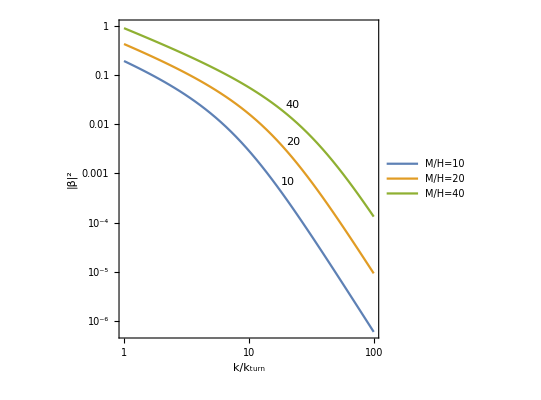

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-2),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)};

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* gęstość energii wyprodukowanych ciężkich cząstek w uproszczonej wersji *)
Block[{mh},(mh={10^(-4), 2*10^(-4), 4*10^(-4), 5*10^(-4), 10^(-3), 2*10^(-3)};
N[mh^4*Sin[Δθ]^2/(16*Pi^2) /. param])]
```

{6.04707×10^-20,9.67531×10^-19,1.54805×10^-17,3.77942×10^-17,6.04707×10^-16,9.67531×10^-15}

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

13:37:41GMT+2.TimeObject[{13,37,41.4347},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

13:37:41GMT+2.TimeObject[{13,37,41.4387},TimeZone→2.] Wykres wierszy 1

13:37:43GMT+2.TimeObject[{13,37,43.3891},TimeZone→2.] Wykres wierszy 2

13:37:43GMT+2.TimeObject[{13,37,43.743},TimeZone→2.] Wykres kolumn 1

13:37:43GMT+2.TimeObject[{13,37,43.9748},TimeZone→2.] Wykres kolumn 2

{2.79838,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

13:48:01GMT+2.TimeObject[{13,48,1.50801},TimeZone→2.] Liczba e-powiększeń i baza

13:48:01GMT+2.TimeObject[{13,48,1.50801},TimeZone→2.] Wykres wierszy 1

13:48:02GMT+2.TimeObject[{13,48,2.10928},TimeZone→2.] Wykres wierszy 2

13:48:02GMT+2.TimeObject[{13,48,2.37875},TimeZone→2.] Wykres kolumn 1

13:48:02GMT+2.TimeObject[{13,48,2.61055},TimeZone→2.] Wykres kolumn 2

{1.34132,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,
Lao,eps,h},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

(* lista współczynników oddziaływania w formie {{C_σs1, C_σs2, ...}, {C_s1σ, C_s1s2, ...}, ...} *)
(*funkcje=Abs[Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,False]/.{H->Symbol["nn"]'}]]+10.^(-6);*)
(*funkcje={Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,False]] // Flatten};
opisy={{"C","coefficients",{"C_σs1","C_s1σ"}}};*)

eps=-Symbol["nn"]''[x[[1]]]/Symbol["nn"]'[x[[1]]]^2;
funkcje={{eps}};
opisy={{"eps","",{"ϵ"}}};

(*funkcje={{Log[pola[[1]][x[[1]]]/L]}};
opisy={{"logfiL","",{Log[ToString[pola[[1]]]/"L"]}}};*)

h=Sqrt[D[V[Sequence@@Map[#[x[[1]]] &,pola]],pola[[1]][x[[1]]]]/(L*Symbol["nn"]'[x[[1]]]^2)-9];
(*h=Sqrt[D[V[Sequence@@Map[#[x[[1]]] &,pola]],pola[[1]][x[[1]]]]/(L*Symbol["nn"]'[x[[1]]]^2)];*)
funkcje={{h}};
opisy={{"h","h",{"h"}}};

(*funkcje={{D[V[Sequence@@Map[#[x[[1]]] &,pola]],{pola[[2]][x[[1]]],2}]/(Symbol["nn"]'[x[[1]]]^2)}};
opisy={{"eta","",{Subscript["3η","ss"]}}};*)

(*funkcje={{h,eps,1-2*eps+0.924*h*3*L/pola[[1]][x[[1]]]}};*)
funkcje={{h,eps,1-2*eps}};
opisy={{"h_eps_ns","",{"h","ϵ",Subscript["n","s"]}}};

WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

00:49:48GMT+2.TimeObject[{0,49,48.2366},TimeZone→2.] Liczba e-powiększeń

00:49:48GMT+2.TimeObject[{0,49,48.2522},TimeZone→2.] Wykres 1

{0.385012,Null}

### Perturbacje

```mathematica
(* widma *)
(* widma w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

13:50:40GMT+2.TimeObject[{13,50,40.5719},TimeZone→2.]

13:50:40GMT+2.TimeObject[{13,50,40.5739},TimeZone→2.] Równania ruchu w rzędzie 1

13:50:43GMT+2.TimeObject[{13,50,43.9397},TimeZone→2.] Równania ruchu w rzędzie 1

13:50:54GMT+2.TimeObject[{13,50,54.7918},TimeZone→2.] Równanie pola 11 w rzędzie 0

13:50:55GMT+2.TimeObject[{13,50,55.0577},TimeZone→2.] Równanie pola 00 w rzędzie 1

13:50:56GMT+2.TimeObject[{13,50,56.9323},TimeZone→2.] Równanie pola 01 w rzędzie 1

13:50:57GMT+2.TimeObject[{13,50,57.4181},TimeZone→2.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

13:52:26GMT+2.TimeObject[{13,52,26.5857},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny (O)

NDSolve`ProcessEquations::ntdv: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

NDSolve`Iterate::sivpd: The first argument mrkRozwiazania`Private`datai to NDSolve`Iterate should be a symbol assigned to a value that is a valid NDSolve`StateData object.

NDSolve::vdobj: Encountered {«1»,Qσkw[0]==48675.5,Qs1kw[0]==0.,Qσkw'[0]==-138.601-272099. ⅈ,Qs1kw'[0]==0.}, which is not a valid NDSolve`StateData expression.

NDSolve`Iterate::sivpd: The first argument mrkRozwiazania`Private`datai to NDSolve`Iterate should be a symbol assigned to a value that is a valid NDSolve`StateData object.

NDSolve::vdobj: Encountered {«1»,Qσkw[0]==48675.5,Qs1kw[0]==0.,Qσkw'[0]==-138.601-272099. ⅈ,Qs1kw'[0]==0.}, which is not a valid NDSolve`StateData expression.

General::stop: Further output of NDSolve::vdobj will be suppressed during this calculation.

13:58:40GMT+2.TimeObject[{13,58,40.8932},TimeZone→2.] Perturbacje ℛ i 𝒮

Transpose::nmtx: The first two levels of {NDSolve`ProcessSolutions[Qσkw[0]==48675.5],NDSolve`ProcessSolutions[Qσkw[0]==48675.5]} cannot be transposed.

13:58:40GMT+2.TimeObject[{13,58,40.9323},TimeZone→2.] Widma

Total::normal: Nonatomic expression expected at position 1 in Total[2].

13:58:40GMT+2.TimeObject[{13,58,40.9468},TimeZone→2.] Liczba e-powiększeń i widma

13:58:40GMT+2.TimeObject[{13,58,40.9568},TimeZone→2.] Wykres widm

Total::normal: Nonatomic expression expected at position 1 in Total[2.].

General::stop: Further output of Total::normal will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {NDSolve`ProcessSolutions[Qσkw[0.]==48675.5],NDSolve`ProcessSolutions[Qσkw[0.]==48675.5]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

13:58:41GMT+2.TimeObject[{13,58,41.6248},TimeZone→2.] Liczba e-powiększeń i widma

13:58:41GMT+2.TimeObject[{13,58,41.6404},TimeZone→2.] Wykres wierszy 1

Part::partd: Part specification (0.00566886681534573378 Abs[Transpose[{NDSolve`ProcessSolutions[Equal[«2»]],NDSolve`ProcessSolutions[Equal[«2»]]}]]^2)⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification (0.00566887 Abs[Transpose[{NDSolve`ProcessSolutions[Equal[«2»]],NDSolve`ProcessSolutions[Equal[«2»]]}]]^2)⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification (0.00552891836438636715 Abs[Transpose[{NDSolve`ProcessSolutions[Equal[«2»]],NDSolve`ProcessSolutions[Equal[«2»]]}]]^2)⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

13:58:42GMT+2.TimeObject[{13,58,42.3262},TimeZone→2.] Wykres wierszy 2

13:58:42GMT+2.TimeObject[{13,58,42.7746},TimeZone→2.] Wykres kolumn 1

13:58:43GMT+2.TimeObject[{13,58,43.3758},TimeZone→2.] Wykres kolumn 2

{483.27,Null}

```mathematica
(* perturbacje w zależności od liczby e-powiększeń *)
PerturbacjeB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},NkwNorm->0.,norm->"",tftot->tfTot,baza->"F",RS->False,pertu->True];//AbsoluteTiming
```

01:03:28GMT+2.TimeObject[{1,3,28.0809},TimeZone→2.] Liczba e-powiększeń i widma

kw 0.0067936528657079158848

tf A {2.52186×10^12,13.3804}

tf {Re,Im} {{1.63101×10^11,1.62659},{4.65185×10^10,0.555018}}

01:03:28GMT+2.TimeObject[{1,3,28.0966},TimeZone→2.] Wykres perturbacji

01:03:29GMT+2.TimeObject[{1,3,29.4531},TimeZone→2.] Wykres wierszy 1

01:03:29GMT+2.TimeObject[{1,3,29.8849},TimeZone→2.] Wykres wierszy 2

01:03:30GMT+2.TimeObject[{1,3,30.3862},TimeZone→2.] Wykres kolumn 1

01:03:30GMT+2.TimeObject[{1,3,30.7869},TimeZone→2.] Wykres kolumn 2

01:03:31GMT+2.TimeObject[{1,3,31.1879},TimeZone→2.] Wykres Re

01:03:31GMT+2.TimeObject[{1,3,31.8707},TimeZone→2.] Wykres Im

{4.67065,Null}

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F",RS->False,pertu->False];//AbsoluteTiming
```

01:07:50GMT+2.TimeObject[{1,7,50.9399},TimeZone→2.]

01:07:50GMT+2.TimeObject[{1,7,50.9711},TimeZone→2.] Liczba e-powiększeń i widma

kw 0.0067936528657079158848

tf {5.23458×10^12,1.4736×10^-10}

01:07:50GMT+2.TimeObject[{1,7,50.9711},TimeZone→2.] Wykres widm

01:07:52GMT+2.TimeObject[{1,7,52.0431},TimeZone→2.] Wykres wierszy 1

01:07:53GMT+2.TimeObject[{1,7,53.0467},TimeZone→2.] Wykres wierszy 2

01:07:53GMT+2.TimeObject[{1,7,53.5457},TimeZone→2.] Wykres kolumn 1

01:07:54GMT+2.TimeObject[{1,7,54.0784},TimeZone→2.] Wykres kolumn 2

{3.67663,Null}

```mathematica
(* widma w bazie Freneta w zależności od liczby falowej *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

16:58:24GMT+2.TimeObject[{16,58,24.4398},TimeZone→2.]

16:58:55GMT+2.TimeObject[{16,58,55.9664},TimeZone→2.] Rozwiązania dla perturbacji

16:59:09GMT+2.TimeObject[{16,59,9.28379},TimeZone→2.] Perturbacje ℛ i 𝒮

16:59:40GMT+2.TimeObject[{16,59,40.0034},TimeZone→2.] Widma

16:59:42GMT+2.TimeObject[{16,59,42.6303},TimeZone→2.] Widma

kNorm 9.99505705695131953×10^-616:59:58GMT+2.TimeObject[{16,59,58.0927},TimeZone→2.]

1: {1.08688}17:01:52GMT+2.TimeObject[{17,1,52.5199},TimeZone→2.]

$Aborted

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby falowej *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,listatf1cf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M"];//AbsoluteTiming
```

{637.133,Null}

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->{"N",0.}];//AbsoluteTiming
```

13:59:53GMT+2.TimeObject[{13,59,53.1757},TimeZone→2.]

13:59:53GMT+2.TimeObject[{13,59,53.1757},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

$Aborted

```mathematica
Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"h",tftot->tfTot];//AbsoluteTiming
```

01:40:34GMT+2.TimeObject[{1,40,34.8096},TimeZone→2.]

01:40:34GMT+2.TimeObject[{1,40,34.8252},TimeZone→2.] Korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8428},TimeZone→2.] Liczba e-powiększeń i korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8443},TimeZone→2.] Wykres

{1.56311,Null}

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2, k2/k1} *)
Block[{Nkw},(Nkw=3.;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{9.995063188024065092×10^-6,0.00020073747824086946889,-0.0001907424150528454038,20.083662750765808735}

```mathematica
(* liczby obsadzeń *)
(* liczba obsadzeń w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},NkwNorm->0.,zakrest->tzakresB];//AbsoluteTiming
```

21:52:07GMT+2.TimeObject[{21,52,7.68142},TimeZone→2.]

21:52:07GMT+2.TimeObject[{21,52,7.69703},TimeZone→2.] Liczba e-powiększeń i liczba obsadzeń

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0432705,0.},{0.,7.00679×10^10}} may contain significant numerical errors.

{1.41403×10^-6,6.54512×10^23}21:52:07GMT+2.TimeObject[{21,52,7.7619},TimeZone→2.]

{5.56832×10^39,2.582×10^41}21:52:07GMT+2.TimeObject[{21,52,7.80879},TimeZone→2.]

InterpolatingFunction::dmval: Input value {20000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.88032×10^40,3.56014×10^44}21:52:08GMT+2.TimeObject[{21,52,8.77194},TimeZone→2.]

21:52:08GMT+2.TimeObject[{21,52,8.77244},TimeZone→2.] Wykres

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0432685,0.},{0.,6.86585×10^10}} may contain significant numerical errors.

$Aborted

```mathematica
(* liczba obsadzeń w zależności od liczby falowej *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,zakrest->{tB}];//AbsoluteTiming
```

15:39:29GMT+2.TimeObject[{15,39,29.6023},TimeZone→2.]

15:39:29GMT+2.TimeObject[{15,39,29.6179},TimeZone→2.] Liczba obsadzeń

kwNorm: {0.400662,0.492885}15:39:30GMT+2.TimeObject[{15,39,30.3355},TimeZone→2.]

1.5: {1.41673,0.233238}15:39:58GMT+2.TimeObject[{15,39,58.7464},TimeZone→2.]

2: {0.201874,0.148739}15:40:30GMT+2.TimeObject[{15,40,30.5578},TimeZone→2.]

$Aborted

```mathematica
Test
(* gęstość energii wyprodukowanych na zakręcie cząstek w chwili t0 *)
Print[TimeObject[Now]];
GestoscEnergiiCzastekTest[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS, t0->tN0]//AbsoluteTiming
```

Test

04:56:04GMT+2.TimeObject[{4,56,4.98974},TimeZone→2.]

04:56:13GMT+2.TimeObject[{4,56,13.7468},TimeZone→2.] Gęstości energii wyprodukowanych cząstek

{{0.000099552,0},{0,0.00098715}}

{9.9951×10^-6,{0.00010005,0.0009872}}

4.45893×10^-14

8.78729×10^-14

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny *)
Print[TimeObject[Now]];
IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.01},baza->"F"]//AbsoluteTiming
```

16:00:51GMT+2.TimeObject[{16,0,51.9968},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny *)
Print[TimeObject[Now]];
IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.5},baza->"F"]//AbsoluteTiming
```

01:16:05GMT+2.TimeObject[{1,16,5.17339},TimeZone→2.]

01:17:13GMT+2.TimeObject[{1,17,13.3951},TimeZone→2.] Perturbacje ℛ i 𝒮

01:17:13GMT+2.TimeObject[{1,17,13.3951},TimeZone→2.] Widma

{68.2373,{0.0067936528657079158848,0.011117567319103898093,-0.004323914453395982208,{0.972881,10.1206}}}

```mathematica
(* 1 *)
(* N2=0.001 *)
{0.00679365286570791588484787270578215677`20.457636070172022,0.00680035643887221628804824791949710407`20.49264605103474,-6.7035731643004032003752137149473`17.167755790107073*^-6,{1.5241848278346688,9.165819519674459}}
(* N2=0.005 *)
{0.00679365286570791588484787270578215677`20.457636070172022,0.00682719479958960766448258052358542344`20.695116845277056,-0.00003354193388169177963470781780326667`17.952011741955825,{0.9126646609635909,4.112715586927301}}
 (* N2=0.01 *)
{0.00679365286570791588484787270578215677`20.457636070172022,0.00686091359621174595051237207704717455`21.600618430819306,-0.00006726073050383006566449937126501778`18.42283215489661,{0.9923634293621566,4.198087586990129}}
 (* N2=0.1 *)
{0.00679365286570791588484787270578215677`20.457636070172022,0.00749695680834262166384777774653753418`20.277405965638668,-0.00070330394263470577899990504075537741`19.045979790704994,{0.9687380815891055,5.3721316290846675}}
(* N2=0.5 *)
{0.00679365286570791588484787270578215677`20.457636070172022,0.01111756731910389809277659832544931868`20.602182140030752,-0.00432391445339598220792872561966716191`19.92431643553136,{0.9728805188102219,10.120647363085343}}
```

```mathematica
(* 2 *)
(* N2=0.001 *)
{0.00187525569538664047978385840629213199`20.00724059262225,0.00187701392543696687871969798906334199`20.085228796156485,-1.75823005032639893583958277121001`16.715286339527722*^-6,{1.045558884781883,4.7627712305915}}
(* N2=0.005 *)
{0.00187525569538664047978385840629213199`20.00724059262225,0.00188404890418233778852003833831531872`19.914069808679056,-8.79320879569730873617993202318674`17.327092777288545*^-6,{2.613652852051472,8.264739317117447}}
 (* N2=0.01 *)
{0.00187525569538664047978385840629213199`20.00724059262225,0.00189288028985392735592144228656258892`20.20655050296475,-0.00001762459446728687613758388027045694`17.766011793607177,{2.6160448719960483,3.697030156372605}}
 (* N2=0.1 *)
{0.00187525569538664047978385840629213199`20.00724059262225,0.00205909411948248384772112081256552408`20.21510801511536,-0.00018383842409584336793726240627339209`18.773210202505,{2.6616343804532647,2.7179337565511954}}
(* N2=0.5 *)
{0.00187525569538664047978385840629213199`20.00724059262225,0.00299196351859868509421394481320625263`20.082260609002745,-0.00111670782321204461443008640691412064`19.412462128489608,{2.9386754986960035,2.7363138766848594}}
```

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",Nk},baza->"F"];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.}, NkwNorm->0.];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
(*wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];*)
wartosci=Flatten[{Map[ScientificForm[If[Element[#[[2]],Rationals],N[#[[2]]],#[[2]]], 2, NumberMultiplier->"*",NumberPoint->","] &, param], {NumberForm[N0t,NumberPoint->","],NumberForm[N0p,NumberPoint->","]},Map[ScientificForm[If[Element[#,Rationals],N[#],#], 3, NumberMultiplier->"*",NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=nazwaplikurow<>"_dane.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

01:17:58GMT+2.TimeObject[{1,17,58.0451},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny (O)

NDSolve`ProcessEquations::underdet: There are more dependent variables, {H[t],Qs1kw[t],Qσkw[t]}, than equations, so the system is underdetermined.

NDSolve`Iterate::sivpd: The first argument mrkRozwiazania`Private`datai to NDSolve`Iterate should be a symbol assigned to a value that is a valid NDSolve`StateData object.

NDSolve::vdobj: Encountered {«1»}, which is not a valid NDSolve`StateData expression.

$Aborted

```mathematica
Quit[]
```